# Running in the Rain

## Predicting Runs based on Environmental Data

Stephen Schroeder

## Introduction

I have been running for several years now, and in September of 2017 I decided that I would start a "run streak." A running streak is defined as running at least 1 mile (1.61 km) every calendar day consecutively. I did this mostly because I found that I couldn't stick to only running 3 or 4 days a week - I would suddenly find myself not having run for several weeks or months! 

Now, almost two years later I have ideas about things that might affect my running, but Wolfram Language allows for so much interesting analysis to be done with my data tracked using RunKeeper! Normally I don’t go out with a plan for how long I will run, and I turn back based on how I am feeling that day. Because of this, one of the main questions that I have about my running data is how my running is affected by temperature. I know that I run less in the Canadian winter, but exactly how much less?

## Running Data Preparation

### Importing Running Data

Previously, I used ServiceConnect to fetch my running data, but unfortunately ServiceConnect does not fetch GPS data from RunKeeper which I will need to be able to get environmental data based on the location, date, and time of my run. 
So, I manually exported my data from my RunKeeper account as explained here, and saved the data to my NotebookDirectory[] with all the GPS files in their own folder. Now, to get started, all the data needs to be imported. I imported the data in a similar fashion to this fantastic Wolfram Blog post, where the running data is parsed using the smart SemanticImport using the column types of the .csv file from RunKeeper.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
runningData = SemanticImport[
	"cardioActivities.csv",
	{"String","Date","String","String",Restricted["Quantity","Kilometers"],
	"String","String",Restricted["Quantity",("Kilometers")/("Hours")],Restricted["Quantity","LargeCalories"],
	Restricted["Quantity","Meters"],"String","String","String","String"
	}
];
```

The GPS Data is slightly more difficult to work with, as each of the 651 runs that I exported have their own .GPX file, and to best deal with the data I only want the coordinates that were recorded at the very beginning of the run.

```mathematica
importGPSData[] := importGPSData[FileNames["*.gpx", "GPS"]]
importGPSData[files_List] := Association@ Map[importGPSData, files]
importGPSData[file_String] :=FileNameTake[file] ->  First @ Cases[
Import[file, "XML"], XMLElement["trkpt",{"lat"->lat_,"lon"->lon_},{_,XMLElement["time",{},{time_}]}] :> {time, lat, lon}, 
Infinity
];

rawGPSData = importGPSData[];
```

Now, so I can best use the GPS data, I will make sure that it is explicitly made up of lists of GeoPositions

```mathematica
GPSData = Map[
GeoPosition@{ToExpression[#[[2]]], ToExpression[#[[3]]]} &, 
rawGPSData
];
```

Lastly, the data needs to be added alongside the rest of the running data imported earlier into our now nice looking dataset!

```mathematica
runningDataWithGPS = Map[
Append[#, "GeoCoord" -> GPSData[#["GPX File"]]]&,
runningData
];
```

### Getting Date-time and Location Specific Temperatures

In order to discover how temperature affects how long I run, I first need to get the data. Thankfully Location and Time-Specific Data is available using the Wolfram Language’s integrated knowledge. I’ll also clean up some missing GPS data to avoid errors.

```mathematica
coords = DeleteCases[Values@Normal@runningDataWithGPS[[All, {"GeoCoord", "Date"}]], {_Missing, _}];
tempData = AirTemperatureData[coords];
```

Finally, all that needs to be done is to add this data to the dataset!

```mathematica
tempDataAssoc = AssociationThread[coords -> tempData];
```

```mathematica
runningDataWithGPSandTemp = Map[
Append[#, "Temperature" -> tempDataAssoc[{#["GeoCoord"],#["Date"]}]]&,
runningDataWithGPS
];
```

```mathematica
DumpSave["fullrundata.mx",{runningDataWithGPSandTemp,coords,tempDataAssoc,tempData}];
```

```mathematica
Get["fullrundata.mx"];
```

## Data Visualisation and Evaluation

Now it' s possible to do tons of analysis of my running data! First, we can see the starting locations of my runs over the past  2 years. Lots of running in icy Canada.

```mathematica
geodata = Flatten[
			Cases[coords,GeoPosition[place__]:>{place},Infinity]
				,1];
```

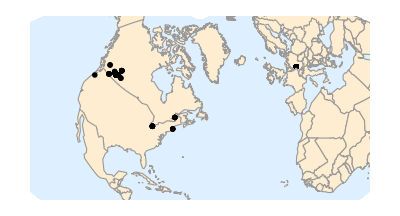

```mathematica
GeoGraphics[GeoMarker[geodata],GeoBackground->"CountryBorders"]
```

The next plot provides real evidence that those cold winters do cause my running distance to go down! It seems like there must be some correlation there.

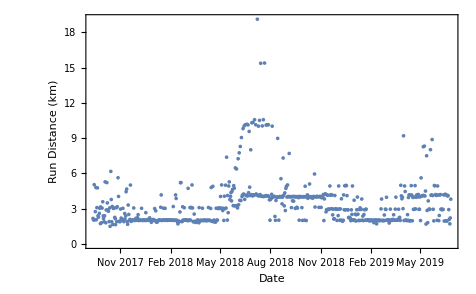

```mathematica
DateListPlot[Query[All,{"Date","Distance (km)"}]@runningDataWithGPSandTemp,Axes->True,FrameLabel->{"Date","Run Distance (km)"},Joined->False,PlotRange->All]
```

### Distance as a function of temperature

This is what everything has been building to! To visualise the data, all that needs to be done is pair the temperature at the time and location of my run with the distance of my run:

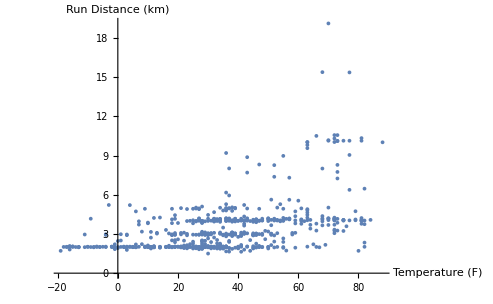

```mathematica
ListPlot[Query[All,{"Temperature","Distance (km)"}]@runningDataWithGPSandTemp,AxesLabel->{"Temperature (F)","Run Distance (km)"},PlotRange->All]
```

Looking at this data, there doesn’t seem to be a strong correlation between the temperature and how far I run, but it’ll still be possible to make a predictive function!

## How Far Will I Run in the Rain, Snow, or Shine?

Now that all the work is done, we can train an algorithm on my running data, and get a predictor function out of it! We just have to feed in the data as a nice, clean list of rules to make sure we get something that makes sense.

```mathematica
tempdistassoc=Cases[runningDataWithGPSandTemp//Normal//Values,{__,Quantity[distance_,"Kilometers"],__,Quantity[temperature_,"DegreesFahrenheit"]}:>{temperature->distance},Infinity];
```

```mathematica
distpredict=Predict[Flatten[tempdistassoc]]
```

PredictorFunction[…]

```mathematica
distpredict["Information"]
```

PredictorFunction::mlincfttp: Incompatible variable type (Numerical) and variable value (Information).

PredictorFunction[…][Information]

```mathematica
distpredict[-20]
```

1.43806

```mathematica
Show[Plot[distpredict[x],{x,-20,90},Exclusions->None],ListPlot[tempdistassoc]]
```

-Graphics-

```mathematica
ListPlot[tempdistassoc]
```

$Aborted[]